```mathematica
Series[Sin[x],{x,0,3}]
```

x-x^3/6+O[x]^4

```mathematica
Normal[Series[Sin[x],{x,0,3}]]
```

x-x^3/6

```mathematica
N[Pi,20]
```

3.1415926535897932385

```mathematica
f[x_] = x^2+3*x-5;
Solve[f[x]==0,x]
```

{{x→1/2 (-3-√29)},{x→1/2 (-3+√29)}}

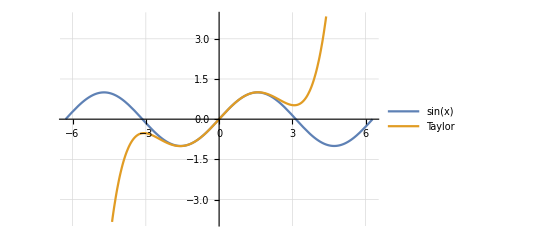

```mathematica
Normal[Series[Sin[x], {x,0,5}]];
Plot[{Sin[x],%},{x,-2*Pi,2*Pi}, PlotLegends->{"sin(x)","Taylor"}, GridLines->Automatic]
```

```mathematica
ClearAll["Global`*"]
Ctot[q_] = a*(d/q)+b*(q/2)
der = D[Ctot[q],q]
```

(a d)/q+(b q)/2

b/2-(a d)/q^2

```mathematica
Solve[der == 0, q]
qq = %[[2,1,2]]
```

{{q→-(√2 √a √d)/(√b)},{q→(√2 √a √d)/(√b)}}

(√2 √a √d)/(√b)

```mathematica
a*(d/qq)+b*(qq/2)
```

√2 √a √b √d

```mathematica
ClearAll["Global`*"]
f[x_,y_] = 100*(y-x^2)^2+(a-x)^2;
grad = D[f[x,y],{{x,y}}];
min = Solve[grad=={0,0},{x,y}]
f[x,y] /. {x->min[[1,1,2]],y->min[[1,2,2]]}
```

{{x→a,y→a^2}}

0

```mathematica
a = 1;
pic = Plot3D[f[x,y], {x,0,2},{y,0,2}]
```

-Graphics3D-

```mathematica
ClearAll["Global`*"]
f[a_,b_]=(a*b)/(a+b);
grad = D[f[a,b],{{a,b}}];
agrad = Abs[grad];
errorAB = {da, db};
errorF = Simplify[agrad.errorAB]
a = 85;
da = 1;
b = 196;
db = 2;
F = f[a,b]
N[%]
{F-errorF,F+errorF}
N[%]
```

db Abs[a^2/(a+b)^2]+da Abs[b^2/(a+b)^2]

16660/281

59.2883

{4628594/78961,4734326/78961}

{58.6187,59.9578}

```mathematica
ClearAll["Global`*"]
A[r_,p_] = (1/2)*p*r^2;
grad = D[A[r,p], {{r,p}}];
agrad = Abs[grad];
errorRP = {dr,dp};
errorA=Simplify[agrad.errorRP]
deltaR=Solve[errorA==dA,dr]
deltaR /. {dA->(1/2), dp->(1/100)*(2*Pi/360)};
Expand[%];
Simplify[%]
deltaR /. {dA-> (1/2), r-> 50, p-> 2*Pi/3,
dp-> (1/100)*(2*Pi/360)};
Simplify[%]
N[%]
```

1/2 dp Abs[r]^2+dr Abs[p r]

{{dr→(2 dA-dp Abs[r]^2)/(2 Abs[p r])}}

{{dr→(18000-π Abs[r]^2)/(36000 Abs[p r])}}

{{dr→-1/480+3/(200 π)}}

{{dr→0.00269131}}